## Problem 1

```mathematica
Remove["Global`*"]
HankelTransformQ2θ[f_,assume_]:=2π Integrate[f q BesselJ[0,2π θ q],{q,0,∞},Assumptions-> assume]
HankelTransformθ2Q[f_,assume_]:=2π Integrate[f θ BesselJ[0,2π θ q],{θ,0,∞},Assumptions-> assume]
NHankelTransformQ2θ[f_]:=2π NIntegrate[f q BesselJ[0,2π θ q],{q,0,∞}]
NHankelTransformθ2Q[f_]:=2π NIntegrate[f θ BesselJ[0,2π θ q],{θ,0,∞}]
dish=Piecewise[{{1, q^2<(B/λ)^2}, {0, True}}];
Print["Evenly illuminated aperture with diameter D"]
Print[TraditionalForm[dish/.B->D]]
Print["Apply Fourier Transform for Single Dish"]
s[θ_]=1/(2π)Integrate[dish Exp[ⅈ 2 π θ q],{q,0,∞},Assumptions->{B>0,q>0,λ>0}];
singledish[θ_]=Assuming[B>0 && λ>0,Simplify[s[θ]/Limit[s[θ],θ->0]]];
Print["G_singledish[θ]= ",TraditionalForm[%/.B->D]]
i[θ_]=HankelTransformQ2θ[dish,{B>0,q>0,λ>0}];
Print["Apply Hankel Tranform for Interferometer"]
interferometer[θ_]=Assuming[B>0 &&λ>0,Simplify[i[θ]/Limit[i[θ],θ->0]]];
Print["G_interferometer[θ]= ",TraditionalForm[%/.B->D]]
λ=1;
B=1;
a=θ/.NMinimize[{(Abs[singledish[θ]]-1/2)^2 ,0<θ<2},θ][[2,1]];
Print["Single Dish FWHM = ",2%,"λ/D"]
b=θ/.NSolve[{Abs[interferometer[θ]]==1/2,-1<θ<1},θ][[2]];
Print["Interferometer FWHM ",2%,"λ/D"]
Plot[{Abs[singledish[θ]],Abs[interferometer[θ]]},{θ,-π,π},PlotRange->All,PlotStyle->{{Thick,Red},{Thick,Blue}},PlotLabel->"Single Dish vs Interferometry",AxesLabel->{"θ",""},GridLines->{{-a,a,-b,b},None},ImageSize->575]
```

I might think that the difference has something to do with the fact that in an interferometer, the beam is coming in from multiple receivers

## Problem 2

```mathematica
Remove["Global`*"]
```

Big telescope with aperture D vs N small telescopes with aperture d and total collecting area πD^2

a) Time to SNR ≃ 3   SNR = ΔT/T_A , T_A= (T_B(Ω_S/Ω_B))^2

```mathematica
ΔT=(Subscript[T, R]+Subscript[T, A])/(√(B τ))
Subscript[T, A]=Subscript[T, B](Subscript[Ω, S]/Subscript[Ω, B])^2
SNR=Subscript[T, A]/ΔT
Solve[1/SNR ==1/n,τ]
```

```mathematica
Plot[AiryAi[z],{z,-10π,10π}]
```

## Problem 3

/Users/johnlewisiii/SkyDrive/Mathematica

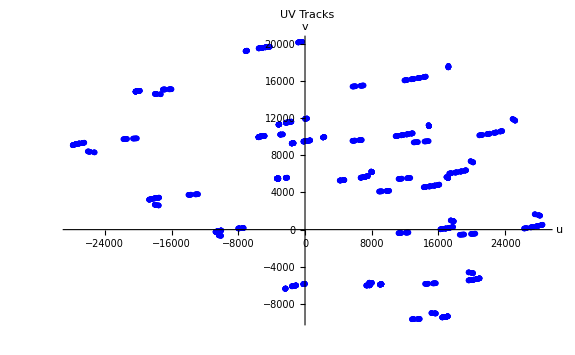

```mathematica
Remove["Global`*"]
XY[x_,y_]:=MapThread[List,{x,y}]
XYZ[x_,y_,z_]:=MapThread[List,{x,y,z}]
hour=15 °;
arcsec=π/(180 60 60);
c=2.998 10^10;
ν=231.62 10^9;
λ=c/ν;
SetDirectory[NotebookDirectory[]]
data=Import["tableGRB1.csv"];
tag=data⟦All,1⟧;
UT=data⟦All,3⟧;
HA=data⟦All,4⟧;
HS=HA hour;
δS=(-5+1/60 (47+36.524/60)) °;
αs=(12+1/60 (56+11.501/60)) hour;
HB=5 hour;
H=HS-HB;
δB=42 °;
az=data⟦All,5⟧;
el=data⟦All,6⟧;
basenumber=data⟦All,7⟧;
u=((10^2 data⟦All,8⟧) Cos[δB] Sin[H])/λ;
v=((10^2 data⟦All,9⟧) (Sin[δB] Cos[δS]-Cos[δB] Sin[δS] Cos[H]))/λ;
w=data⟦All,10⟧ (Sin[δB] Sin[δS]+Cos[δB] Cos[δS] Cos[H]);
ndata=Dimensions[u]⟦1⟧;
amp=data⟦All,11⟧;
phs=data⟦All,12⟧;
ComplexVis=MapThread[(#1 Exp[ⅈ #2 °])&,{amp,phs}];
vis=Sort[XYZ[u,v,amp Exp[ⅈ phs °]]];
uv=XY[u,v];
beam=(Exp[2 π ⅈ #1.{α,β}]&)/@uv;
image=ComplexVis beam;
beam=Total[beam];
image=Total[image];
arcbeam=beam/.α->α arcsec/.β->β arcsec;
arcimage=image/.α->α arcsec/.β->β arcsec;
ListPlot[XY[u,v],PlotStyle->{Thick,Blue},PlotLabel->Style["UV Tracks",20],ImageSize->575,AxesLabel->{"u","v"}]
```

```mathematica
GraphicsRow[{Plot3D[Abs[arcbeam],{α,-20,20},{β,-20,20},PlotRange->All,ColorFunction->"StarryNightColors"],
Plot3D[Abs[arcimage],{α,-20,20},{β,-20,20},PlotRange->All,ColorFunction->"StarryNightColors",AxesLabel->{"α","β","I"}]},ImageSize->Large]
```

-Graphics-

```mathematica
NMaximize[{Abs[arcimage],-20<α<0,0<β<20},{α,β}];
{αo,βo}={α,β}/.Last[%];
maxarcimage=First[%%];
```

```mathematica
centroidbeam=arcbeam/.α->(α-αo)/.β->(β-βo);
maxarcbeam=arcbeam/.α->0/.β->0;
```

```mathematica
scaledbeam=centroidbeam(maxarcimage/maxarcbeam);
Plot3D[{Abs[scaledbeam],Abs[arcimage]},{α,-20,20},{β,-20,20},PlotStyle->{{Red,Opacity[.5]},{Blue,Opacity[.3]}},PlotRange->All,AxesLabel->{"α","β","I"},Mesh->None,PlotPoints->20,MaxRecursion->2]

cleanedimage=arcimage-scaledbeam;
Plot3D[{Abs[cleanedimage],Abs[arcimage]},{α,-20,20},{β,-20,20},PlotStyle->{{Red,Opacity[.5]},{Blue,Opacity[.3]}},PlotRange->All,AxesLabel->{"α","β","I"},Mesh->None]
(*Do[
{αo,βo}={α,β}/.NMaximize[{Abs[cleanedimage],-20<α<20,-20<β<20},{α,β}][[2]];
Print[{αo,βo}];
shiftarcbeam=arcbeam/.α->(α-αo)/.β->(β-βo);
cleanedimage=cleanedimage-shiftarcbeam((cleanedimage/.α->αo/.β->βo)/(shiftarcbeam/.α->αo/.β->βo));
,{i,1,7}]


*)
```

-Graphics3D-

-Graphics3D-

```mathematica
{αo,βo}={α,β}/.NMaximize[{Abs[cleanedimage],-20<α<20,-20<β<20},{α,β}][[2]];
shiftarcbeam=arcbeam/.α->(α-αo)/.β->(β-βo);

cleanedimage=cleanedimage-shiftarcbeam((cleanedimage/.α->αo/.β->βo)/(shiftarcbeam/.α->αo/.β->βo));
```

-Graphics3D-

```mathematica
ndata=Dimensions[u][[1]];
amp=data[[All,11]];
phs=data[[All,12]];
ComplexVis=amp Exp[ⅈ  phs Degree];
vis=Sort[XYZ[u,v,amp Exp[ⅈ phs Degree]]];
uvplane=Table[(*w[[i]]*)DiracDelta[x-u[[i]],y-v[[i]]],{i,1,ndata}];
beam =FourierTransform[uvplane, {x, y}, { α, β},FourierParameters->{-1,2π}];
beam=Exp[2π ⅈ (#1 x + #2 y)]
beam=Total[beam];
Print["beam done"]
visplane=Table[ComplexVis[[i]] DiracDelta[x - u[[i]], y - v[[i]]],{i,1,ndata}]//Simplify;
image = FourierTransform[visplane, {x, y}, {α,β},FourierParameters->{-1,2π}];
image=Total[image];
Print["image done"]
arcimg=image/.α->(α arcsec)/.β->(β arcsec);
arcbeam=beam/.α->(α arcsec)/.β->(β  arcsec);
Print["Done With All Beam Stuff"]
```

beam done

image done

Done With All Beam Stuff

Displaying Beam and Image

-Graphics3D-

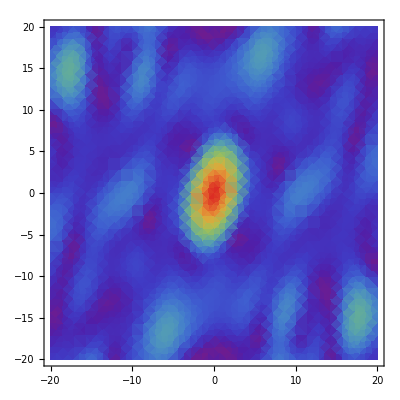

-Graphics3D-

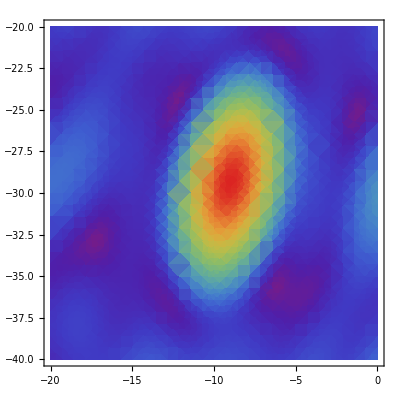

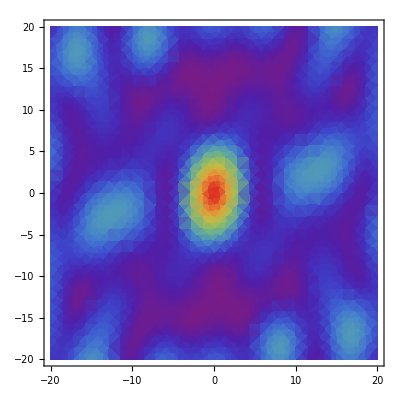

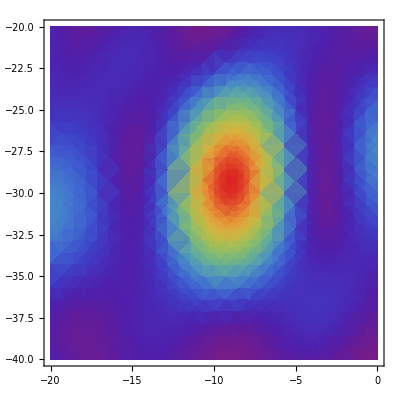

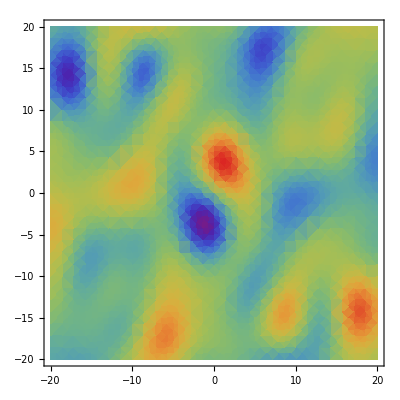

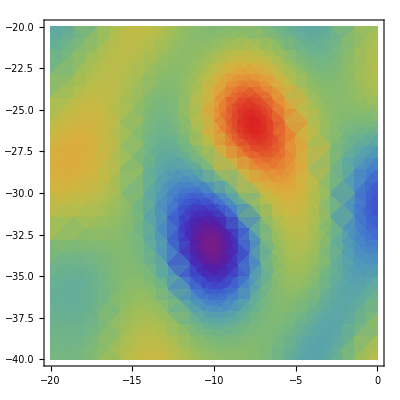

```mathematica
Print["Displaying Beam and Image"]
Plot3D[Abs[arcbeam],{α,-20,20},{β,-20,20},PlotRange->All,ColorFunction->"Rainbow"]
DensityPlot[Abs[arcbeam],{α,-20,20},{β,-20,20},PlotRange->All,ColorFunction->"Rainbow"]
Plot3D[Abs[arcimg],{α,-20,0},{β,-20,-40},PlotRange->All,ColorFunction->"Rainbow"]
DensityPlot[Abs[arcimg],{α,-20,0},{β,-20,-40},PlotRange->All,ColorFunction->"Rainbow"]
DensityPlot[Re[arcbeam],{α,-20,20},{β,-20,20},ColorFunction->"Rainbow",PlotRange->All]
DensityPlot[Re[arcimg],{α,-20,0},{β,-20,-40},ColorFunction->"Rainbow",PlotRange->All]
DensityPlot[Im[arcbeam],{α,-20,20},{β,-20,20},ColorFunction->"Rainbow",PlotRange->All]
DensityPlot[Im[arcimg],{α,-20,0},{β,-20,-40},ColorFunction->"Rainbow",PlotRange->All]
```

Getting PSFs for centroiding

PSFα Done

PSFβ Done

{A→9421.59,σ→2.04983,μ→-9.07233,d→202.415}

{A→13174.8,σ→3.13496,μ→-29.1152,d→390.216}

Offsets Complete

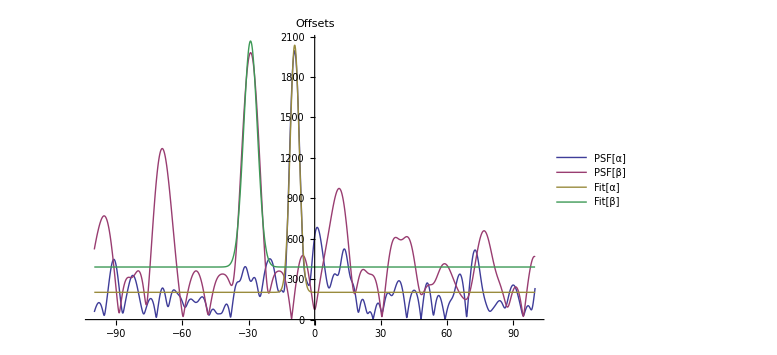

```mathematica
Print["Getting PSFs for centroiding"]
(*arcimsamp={};
DensityPlot[(AppendTo[arcimsamp,{α,β,#}];#)&[arcimg],{α,-100,100},{β,-100 ,100 },PlotLabel->"Image Phase Residuals",ColorFunction->"Rainbow",DisplayFunction->Identity,PlotRange->All]
ListDensityPlot[Abs[arcimsamp],InterpolationOrder->0,ColorFunction->"Rainbow",PlotRange->All]
arcinter=Interpolation[arcimsamp];
psfα:=Sum[arcinter[θ,i],{i,45,55}]
psfα:=Sum[arcinter[i,θ],{i,45,55}]*)
Table[{θ,arcimg/.α->θ/.β->-30},{θ,-100,100,1}];
psfα=Interpolation[%];
Print["PSFα Done"]
Beep[]
Table[{θ,arcimg/.β->θ/.α->-8.5},{θ,-100,100,1}];
psfβ=Interpolation[%];
Print["PSFβ Done"]
Beep[]
nlmα=NonlinearModelFit[Table[{θ,Abs[psfα[θ]]},{θ,-100,100,.02}],A PDF[NormalDistribution[μ,σ],θ]+d,{{A,2000},σ,{μ,-8.5},d},θ];
%["BestFitParameters"]
αo=μ/.%;
nlmβ=NonlinearModelFit[Table[{θ,Abs[psfβ[θ]]},{θ,-100,100,.02}],A PDF[NormalDistribution[μ,σ],θ]+d,{{A,2000},σ,{μ,-30},d},θ];
%["BestFitParameters"]
βo=μ/.%;
Print["Offsets Complete"]
Plot[{Abs[psfα[θ]],Abs[psfβ[θ]],Normal[nlmα],Normal[nlmβ]},{θ,-100 ,100 },PlotStyle->Thick,PlotRange->All,PlotLegends->{"PSF[α]","PSF[β]","Fit[α]","Fit[β]"},PlotLabel->"Offsets",ImageSize->575]
```

Finding Offsets

Normalizing and beam and image and applying centering offsets

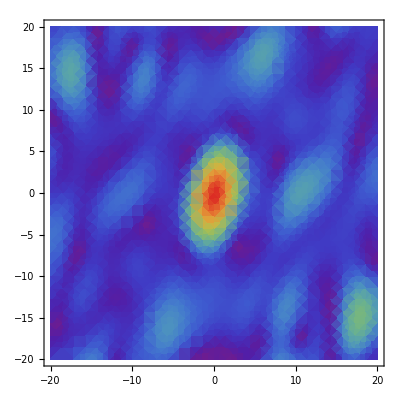

-Graphics-

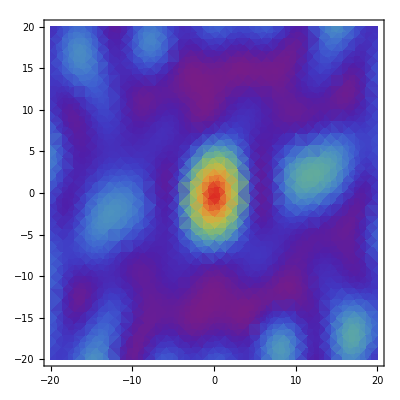

-Graphics-

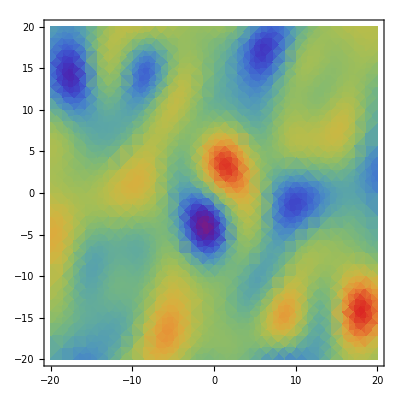

-Graphics-

```mathematica
Print["Finding Offsets"]
Print["Normalizing and beam and image and applying centering offsets"]
carcimg=(arcimg/.α->(α+αo)/.β->(β+βo));/(arcimg/.α->αo/.β->βo);
DensityPlot[Abs[carcimg],{α,-20,20},{β,-20,20},PlotRange->All,ColorFunction->"Rainbow"]
DensityPlot[Abs[arcbeam],{α,-20,20},{β,-20,20},PlotRange->All,ColorFunction->"Rainbow"]
DensityPlot[Re[carcimg],{α,-20,20},{β,-20,20},ColorFunction->"Rainbow",PlotRange->All]
DensityPlot[Re[arcbeam],{α,-20,20},{β,-20,20},ColorFunction->"Rainbow",PlotRange->All]
DensityPlot[Im[carcimg],{α,-20,20},{β,-20,20},ColorFunction->"Rainbow",PlotRange->All]
DensityPlot[Im[arcbeam],{α,-20,20},{β,-20,20},ColorFunction->"Rainbow",PlotRange->All]
```

Getting Phase Residuals

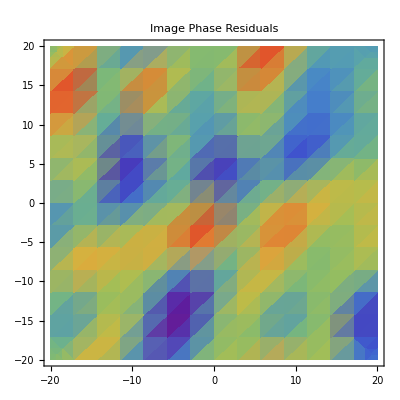

-Graphics-

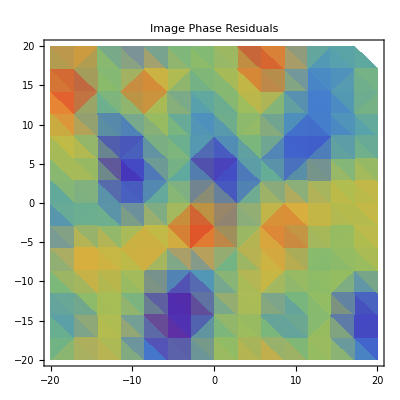

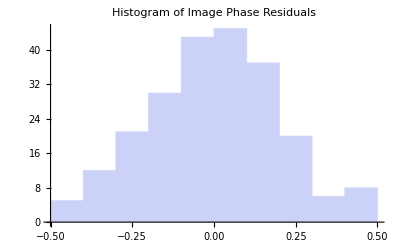

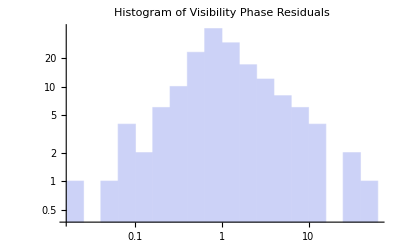

```mathematica
Print["Getting Phase Residuals"]
imresids=(arcimg/(carcimg/.α->0/.β->0))-(arcbeam/(arcbeam/.α->0/.β->0));
DensityPlot[Im[imresids],{α,-20,20},{β,-20 ,20 },PlotLabel->"Image Phase Residuals",ColorFunction->"Rainbow",DisplayFunction->Identity]
samples={};
DensityPlot[(AppendTo[samples,{α,β,#}];#)&[imresids],{α,-20,20},{β,-20 ,20 },PlotLabel->"Image Phase Residuals",ColorFunction->"Rainbow",DisplayFunction->Identity]
phsresids=samples;
XYZ[phsresids[[All,1]],phsresids[[All,2]],Im[phsresids[[All,3]]]];
ListDensityPlot[%,PlotLabel->"Image Phase Residuals",ColorFunction->"Rainbow",DisplayFunction->Identity]
Beep[]
Histogram[Flatten[Im[phsresids[[All,3]]]],PlotLabel->"Histogram of Image Phase Residuals"]
Histogram[Flatten[Im[Fourier[phsresids][[All,3]]]],{"Log","Scott"},{"Log","Count"},PlotLabel->"Histogram of Visibility Phase Residuals"]
Beep[]
Beep[]
```

```mathematica
DensityPlot[Abs[Fourier[imresids]],{α,-100,100},{β,-100 ,100 },PlotLabel->"Image Phase Residuals",ColorFunction->"Rainbow",DisplayFunction->Identity]
```

Fourier::fftl: Argument 0.0517232  - 0.275033\ ⅈ is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument -0.124181 - 0.257562\ ⅈ is not a non-empty list or rectangular array of numeric quantities.

Fourier::fftl: Argument -0.430846 - 0.152272\ ⅈ is not a non-empty list or rectangular array of numeric quantities.

General::stop: Further output of Fourier :: fftl will be suppressed during this calculation.

-Graphics-

## numerically do it

-Graphics-

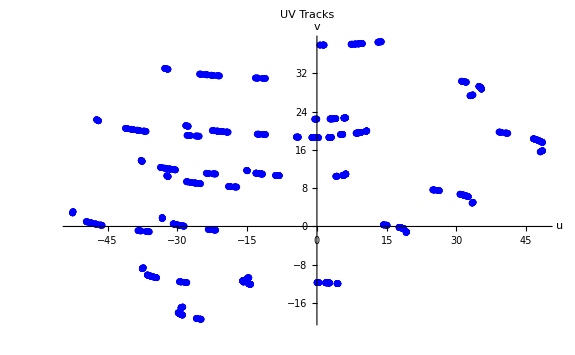

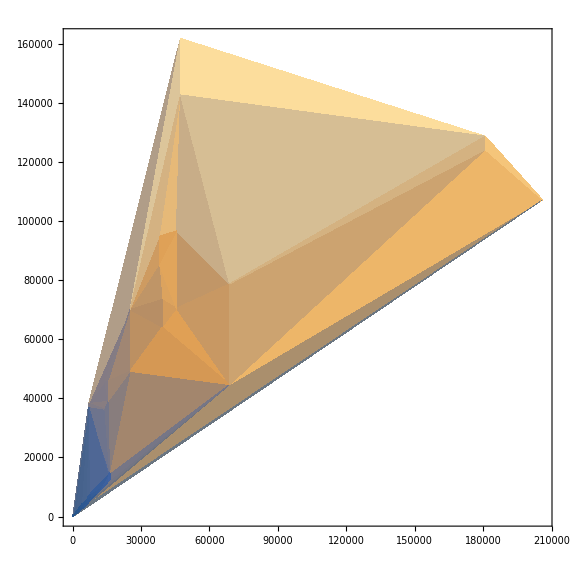

-Graphics-

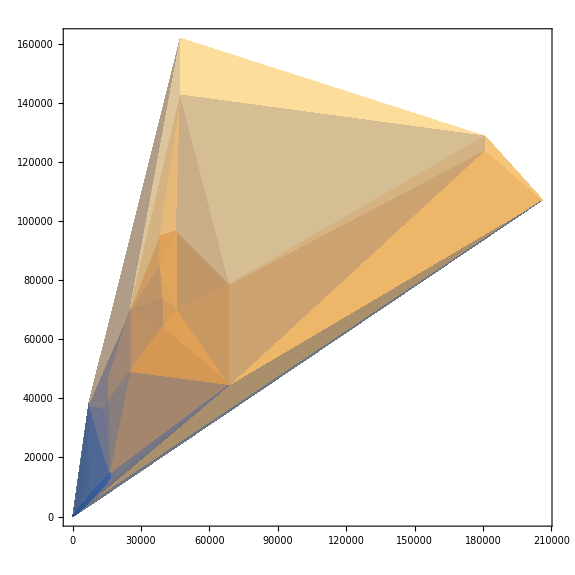

-Graphics-

-Graphics3D-

-Graphics-

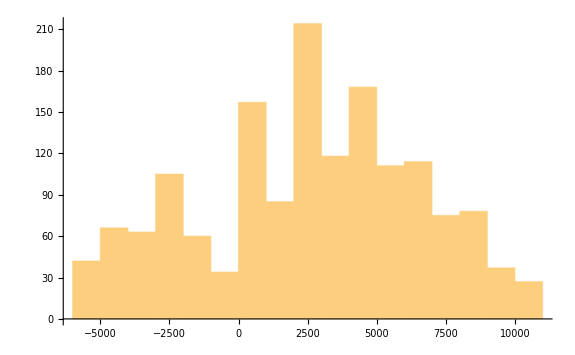

```mathematica
ListPlot[XY[u,v],PlotStyle->{Thick,Blue},PlotLabel->Style["UV Tracks",20],ImageSize->575,AxesLabel->{"u","v"}]
ListPlot[XY[data[[All,8]],data[[All,9]]],PlotStyle->{Thick,Blue},PlotLabel->Style["UV Tracks",20],ImageSize->575,AxesLabel->{"u","v"}]

numimg=Fourier[XYZ[u,v,ComplexVis]];
ListDensityPlot[Abs[numimg]]
nnimg=XYZ[numimg[[All,1]],numimg[[All,2]],Normalize[numimg[[All,3]]]];
ListDensityPlot[Abs[nnimg]]
numbeam=Fourier[XYZ[u,v,v/v]];
ListDensityPlot[Abs[numbeam]]
nnbeam=XYZ[numbeam[[All,1]],numbeam[[All,2]],Normalize[numbeam[[All,3]]]];
ListDensityPlot[Abs[nnbeam]]
diff=XYZ[nnimg[[All,1]],nnimg[[All,1]],nnimg[[All,3]]]-nnbeam[[All,3]];
fdiff=XYZ[nnimg[[All,1]],nnimg[[All,1]],Abs[numimg[[All,3]]-numbeam[[All,3]]]];
ListPlot3D[Abs[diff]]
ListDensityPlot[Abs[fdiff]]
nres=InverseFourier[diff];
Histogram[Im[nres][[All,3]]]
(*phsrshist=HistogramList[Im[%%%%%-%%%][[All,3]],1000];*)
(*SetPrecision[Partition[Riffle[%[[1]],%[[2]]],2],∞];
nnlm=NonlinearModelFit[%, A PDF[GumbelDistribution[α,β],x],{A,α,β},x,MaxIterations->10000]
Variance[GumbelDistribution[α,β]/.%["BestFitParameters"]]
Show[Histogram[Im[nres][[All,3]],1000],Plot[Normal[nnlm],{x,-.00002,.00002},PlotRange->All,PlotStyle->Red],Axes->False,Frame->True,PlotRange->{{-.00001,.00001},{0,155}}]*)
```